```mathematica
sc1=Import["C:\\Users\\matane\\Desktop\\לימודים\\סמסטר ח\\A_ex4_final_movies\\The_Italian_Job\\CSV_files\\AB.csv"];
```

```mathematica
Grid[sc1,Frame->All];
```

------names characters------

```mathematica
Union[sc1[[;;,2]]]
```

{ALL OF THEM,BULLY,BURLY MAN,BUSBOY,CHARLIE,CHRISTINA GRIEGO,CLASSMATE,COUNTER BABE,CUT BACK TO:,DANYA,DETECTIVE,DRIVER,FADE OUT:,FIRST COP,FURIOUS DRIVER,GUARD,HALF-EAR,HANDSOME ROB,"HE WAS ONE OF M'S BEST STUDENTS",HOMEBOY,JOHN BRIDGER,KAREN,KID,LIVING THE GOOD LIFE ON THE PINK SANDS OF BERMUDA,LYLE,MASHKOV,MOTORCYCLE GUARD,OFFICE,PHILLY STEAK,RECEPTIONIST,RICHARD,SECOND COP,SECURITY GUARD,SEVEN YEAR OLD CHARLIE,SKINNY PETE,Speaker,STELLA,STELLA & CHARLIE,STEVE,THE CREW,UKRAINIAN,VALET,WILL THE REAL NAPSTER PLEASE STAND UP,YEVHEN,YOU'LL NEVER SHUT DOWN THE REAL NAPSTER!}

```mathematica
SortBy[Tally[sc1[[;;,2]]],Last]
```

{{ALL OF THEM,1},{BULLY,1},{BURLY MAN,1},{DRIVER,1},{FADE OUT:,1},{GUARD,1},{"HE WAS ONE OF M'S BEST STUDENTS",1},{KID,1},{LIVING THE GOOD LIFE ON THE PINK SANDS OF BERMUDA,1},{MOTORCYCLE GUARD,1},{OFFICE,1},{Speaker,1},{STELLA & CHARLIE,1},{THE CREW,1},{UKRAINIAN,1},{VALET,1},{WILL THE REAL NAPSTER PLEASE STAND UP,1},{YOU'LL NEVER SHUT DOWN THE REAL NAPSTER!,1},{BUSBOY,2},{CLASSMATE,2},{COUNTER BABE,2},{FIRST COP,2},{SECOND COP,2},{FURIOUS DRIVER,3},{HOMEBOY,3},{SEVEN YEAR OLD CHARLIE,3},{CHRISTINA GRIEGO,4},{DETECTIVE,4},{RECEPTIONIST,4},{CUT BACK TO:,5},{DANYA,5},{KAREN,5},{SECURITY GUARD,6},{PHILLY STEAK,7},{RICHARD,9},{SKINNY PETE,9},{YEVHEN,18},{MASHKOV,21},{JOHN BRIDGER,24},{HALF-EAR,40},{STEVE,54},{HANDSOME ROB,55},{LYLE,70},{STELLA,93},{CHARLIE,167}}

```mathematica
ch = sc1[[;;,2]];
```

```mathematica
e1=Table[ch[[i]]<->ch[[i+1]],{i,1,Length[ch]-1}];
e2=Table[ch[[i]]->ch[[i+1]],{i,1,Length[ch]-1}];
```

```mathematica
v1 = Union[ch];
```

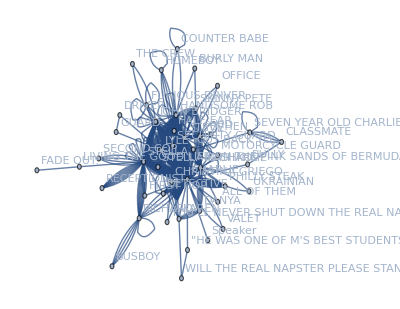

```mathematica
UndirectedWeightedGraph1=Graph[v1,e1,VertexLabels->"Name", ImageSize->Full]
UndirectedNonWeightedGraph2=SimpleGraph[UndirectedWeightedGraph1, ImageSize->Full];
DirectedWeightedGraph3=Graph[v1,e2,VertexLabels->"Name", ImageSize->Full];
DirectedNonWeightedGraph4=SimpleGraph[DirectedWeightedGraph3, ImageSize->Full];
```

THE 4 MAIN CHARACTHERS - italian
VM1our  = what we think
VM1 =  what algo found

```mathematica
VM1our = {"CHARLIE", "STELLA","LYLE" , "STEVE"};
```

```mathematica
PageRankCentrality[UndirectedWeightedGraph1,0.85];
SortBy[Transpose[{VertexList[UndirectedWeightedGraph1],PageRankCentrality[UndirectedWeightedGraph1,0.85]}],Last]
```

{{Speaker,0.00394188},{COUNTER BABE,0.00451983},{VALET,0.00455044},{MOTORCYCLE GUARD,0.0045591},{OFFICE,0.00456777},{KID,0.00459793},{STELLA & CHARLIE,0.00459793},{THE CREW,0.0046075},{FURIOUS DRIVER,0.00461051},{BURLY MAN,0.00474788},{ALL OF THEM,0.00479429},{UKRAINIAN,0.00503815},{YOU'LL NEVER SHUT DOWN THE REAL NAPSTER!,0.00516139},{SECOND COP,0.00573857},{FIRST COP,0.00574581},{HOMEBOY,0.00595752},{BUSBOY,0.00681148},{DRIVER,0.00687732},{GUARD,0.00687732},{"HE WAS ONE OF M'S BEST STUDENTS",0.00715963},{BULLY,0.00722555},{WILL THE REAL NAPSTER PLEASE STAND UP,0.00757116},{FADE OUT:,0.00783649},{RECEPTIONIST,0.0081438},{CHRISTINA GRIEGO,0.00860826},{DETECTIVE,0.00990149},{LIVING THE GOOD LIFE ON THE PINK SANDS OF BERMUDA,0.0105957},{SECURITY GUARD,0.0106631},{CUT BACK TO:,0.011872},{PHILLY STEAK,0.0120969},{DANYA,0.0129839},{KAREN,0.0140586},{SEVEN YEAR OLD CHARLIE,0.0141934},{CLASSMATE,0.0154525},{RICHARD,0.0163678},{SKINNY PETE,0.0173921},{YEVHEN,0.0195596},{JOHN BRIDGER,0.0314793},{MASHKOV,0.0381076},{HALF-EAR,0.0555709},{HANDSOME ROB,0.0739817},{STEVE,0.0755186},{LYLE,0.080381},{STELLA,0.125921},{CHARLIE,0.209055}}

```mathematica
(*{"STEVE",0.07551859691827262},{"LYLE",0.08038103017405371},{"STELLA",0.12592098161421025},{"CHARLIE",0.20905518733434855}*)
VM1 = {"CHARLIE", "STELLA","LYLE" , "STEVE"};
```